Styles

```mathematica
SetOptions[Plot,BaseStyle->FontSize->20];
SetOptions[ContourPlot,BaseStyle->{FontSize->20, FontColor ->  Black}];
SetOptions[ListContourPlot,BaseStyle->{FontSize->20, FontColor ->  Black}];
SetOptions[ListLinePlot,BaseStyle->{FontSize->20, FontColor ->  Black}];
```

## Variables and Definitions

```mathematica
hbar=1.05457148×10(10)^-34; Delta = 40 10^9;Gam = 32.8 10^6/(2 Pi);(*Gamma D2 Line*) 
λ = 852.1 10^-9 (*Red*) ; Inti = 15000;mCs = (133 1.660 10^-27);Er = hbar^2 k^2/(2*mCs) (*Recoil Energy*) ;
alal = 2;k= 2 Pi/λ;
el = 1.602 10^-19;
me = 9.1 10^-31;
λred = 852 10^-9;
γred = 32.8 10^6;
hp = hbar 2 Pi;
Ints = (Pi hp c γred)/(3 λred^3);  (*Saturation Intensity*)

UDsim[x_,y_,z_,a_,b_]:= (*Lattice Potrential*)-1/(12 Delta Ints)Gam^2 hbar Inti (4+Cos[a-b-2 k x]+Cos[a-b+2 k x]+2 Cos[a] Cos[k (x-y)]+2 Cos[b] Cos[k (x+y)]+2 Cos[k (x+z)] Sin[b]+Sin[a+k x-k z]+Sin[a-k x+k z])

ecrosss[x_,y_,z_,a_,b_] := (*Polarization Lattice*)+1/3*hbar Gam^2 Inti / (Delta*8 Ints){-2 (r Cos[k (y+z)]+Sin[a-b] Sin[2 k x]+Sin[a] Sin[k (x-y)]-Sin[b] Sin[k (x+y)]+Cos[a] (r Cos[k (x+z)]-Sin[k (x-z)])-Sin[k (y-z)]+Cos[b] (r Cos[k (x-z)]+Sin[k (x+z)])),2 r (Cos[b] Sin[k (x-z)]-Cos[a] Sin[k (x+z)]-Sin[k (y+z)]),2 r (r+Cos[k z] (Sin[a]-Sin[b]) Sin[k x]+Cos[k x] (Sin[a]+Sin[b]) Sin[k z]+Sin[2 k z])}
Ωrabired[Int_]:= Sqrt[(3 λred^3 γred Int)/(2 Pi hp c)]; (*Rabi frequency red light*)

ecrosssdel[x_,y_,z_,a_,b_, Delta_, Inti_] :=  (*ecrosss function with two additonal parameters: Detuning and Intensity*) +1/3*hbar Gam^2 Inti / (Delta*8 Ints){-2 (r Cos[k (y+z)]+Sin[a-b] Sin[2 k x]+Sin[a] Sin[k (x-y)]-Sin[b] Sin[k (x+y)]+Cos[a] (r Cos[k (x+z)]-Sin[k (x-z)])-Sin[k (y-z)]+Cos[b] (r Cos[k (x-z)]+Sin[k (x+z)])),2 r (Cos[b] Sin[k (x-z)]-Cos[a] Sin[k (x+z)]-Sin[k (y+z)]),2 r (r+Cos[k z] (Sin[a]-Sin[b]) Sin[k x]+Cos[k x] (Sin[a]+Sin[b]) Sin[k z]+Sin[2 k z])}

BeffCouplingDegenerate[θ_, F_]:= Cos[θ]Sum[(1/4 1/F Sqrt[F(F+1)-mF(mF-1)]),{mF, 2, 3}] + Sin[θ] 0 //N;(*matrix elements which couple m and F states in the case of DEGENERATE Raman Sideband cooling (mF<->mF-1)*)
BeffCouplingGenerate[θ_, F_]:= Cos[θ](Sum[-1/4 1/F Sqrt[F(F-1)+mF(mF-1 + 2F)],{mF, -F+2, F}] + Sum[1/4 1/F Sqrt[F(F-1)+mF(mF+1 - 2F)],{mF, -F, F-2}] )+ Sin[θ] Sum[-1/(2 F)Sqrt[F^2-mF^2],{mF, -F+1, F-1}]//N  ;(*matrix elements which couple m and F states in the case of DEGENERATE Raman Sideband cooling (F<->F-1, mF doesnt matter)*)
```

```mathematica
Clear[a,b,x,y,z,r, hbar, Gam, Inti, Ints, Delta,k]
```

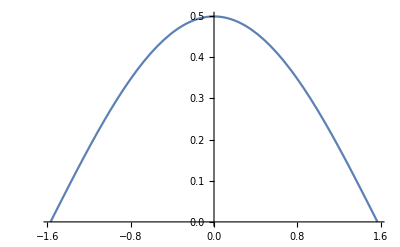

```mathematica
Plot[BeffCouplingDegenerate[θ, 4],{θ,-Pi/2, Pi/2}]
```

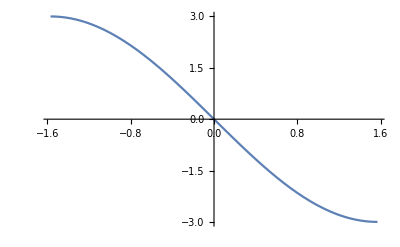

```mathematica
Plot[BeffCouplingGenerate[θ, 4],{θ,-Pi/2, Pi/2}]
```

Stuff (to be ignored by the unaware reader)

```mathematica
UDsim[x_,y_,z_,a_,b_]:=-1/(12 Delta Ints)Gam^2 hbar Inti (4+Cos[a-b-2 k x]+Cos[a-b+2 k x]+2 Cos[a] Cos[k (x-y)]+2 Cos[b] Cos[k (x+y)]+2 Cos[k (x+z)] Sin[b]+Sin[a+k x-k z]+Sin[a-k x+k z])
```

```mathematica
ϵ1 = {r Exp[-ⅈ*k*z], Sin[a]*Exp[ⅈ*k*x]+Sin[b]*Exp[-ⅈ*k*x]+Exp[ⅈ*k*z]+ ⅈ r Exp[-ⅈ*k*z],Cos[a]*Exp[ⅈ*k*x]+Cos[b]*Exp[-ⅈ*k*x]+Exp[ⅈ*k*y] }
ϵ1s = {r Exp[+ⅈ*k*z], Sin[a]*Exp[-ⅈ*k*x]+Sin[b]*Exp[ⅈ*k*x]+Exp[-ⅈ*k*z]- ⅈ r Exp[+ⅈ*k*z],Cos[a]*Exp[-ⅈ*k*x]+Cos[b]*Exp[ⅈ*k*x]+Exp[-ⅈ*k*y]}
```

{ⅇ^(-ⅈ k z) r,ⅇ^(ⅈ k z)+ⅈ ⅇ^(-ⅈ k z) r+ⅇ^(ⅈ k x) Sin[a]+ⅇ^(-ⅈ k x) Sin[b],ⅇ^(ⅈ k y)+ⅇ^(ⅈ k x) Cos[a]+ⅇ^(-ⅈ k x) Cos[b]}

{ⅇ^(ⅈ k z) r,ⅇ^(-ⅈ k z)-ⅈ ⅇ^(ⅈ k z) r+ⅇ^(-ⅈ k x) Sin[a]+ⅇ^(ⅈ k x) Sin[b],ⅇ^(-ⅈ k y)+ⅇ^(-ⅈ k x) Cos[a]+ⅇ^(ⅈ k x) Cos[b]}

```mathematica
ecrossold = +1/3*hbar Gam^2 Inti / (Delta*8 Ints)ⅈ*Cross[{0, Sin[a]*Exp[ⅈ*k*x]+Sin[b]*Exp[-ⅈ*k*x]+Exp[ⅈ*k*z],Cos[a]*Exp[ⅈ*k*x]+Cos[b]*Exp[-ⅈ*k*x]+Exp[ⅈ*k*y]},{0, Sin[a]*Exp[-ⅈ*k*x]+Sin[b]*Exp[ⅈ*k*x]+Exp[-ⅈ*k*z],Cos[a]*Exp[-ⅈ*k*x]+Cos[b]*Exp[ⅈ*k*x]+Exp[-ⅈ*k*y]}]//FullSimplify
```

{1/(12 Delta Ints)Gam^2 hbar Inti (-Sin[a-b] Sin[2 k x]-Sin[a] Sin[k (x-y)]+Sin[b] Sin[k (x+y)]+Cos[a] Sin[k (x-z)]+Sin[k (y-z)]-Cos[b] Sin[k (x+z)]),0,0}

```mathematica
ecrosssold = {1/(12 Delta Ints)Gam^2 hbar Inti (-Sin[a-b] Sin[2 k x]-Sin[a] Sin[k (x-y)]+Sin[b] Sin[k (x+y)]+Cos[a] Sin[k (x-z)]+Sin[k (y-z)]-Cos[b] Sin[k (x+z)]),0,0}
```

{1.73542×10^-28 (-Sin[7.37377×10^6 (x-y)]/(√2)+Sin[7.37377×10^6 y]+Sin[7.37377×10^6 (x+y)]/(√2)),0,0}

```mathematica
+1/3*hbar Gam^2 Inti / (Delta*8 Ints)
```

```mathematica
ecross =  ⅈ*Cross[ϵ1,ϵ1s]//FullSimplify
```

{-2 (r Cos[k (y+z)]+Sin[a-b] Sin[2 k x]+Sin[a] Sin[k (x-y)]-Sin[b] Sin[k (x+y)]+Cos[a] (r Cos[k (x+z)]-Sin[k (x-z)])-Sin[k (y-z)]+Cos[b] (r Cos[k (x-z)]+Sin[k (x+z)])),2 r (Cos[b] Sin[k (x-z)]-Cos[a] Sin[k (x+z)]-Sin[k (y+z)]),2 r (r+Cos[k z] (Sin[a]-Sin[b]) Sin[k x]+Cos[k x] (Sin[a]+Sin[b]) Sin[k z]+Sin[2 k z])}

```mathematica
ecrosss[x_,y_,z_,a_,b_] := +1/3*hbar Gam^2 Inti / (Delta*8 Ints){-2 (r Cos[k (y+z)]+Sin[a-b] Sin[2 k x]+Sin[a] Sin[k (x-y)]-Sin[b] Sin[k (x+y)]+Cos[a] (r Cos[k (x+z)]-Sin[k (x-z)])-Sin[k (y-z)]+Cos[b] (r Cos[k (x-z)]+Sin[k (x+z)])),2 r (Cos[b] Sin[k (x-z)]-Cos[a] Sin[k (x+z)]-Sin[k (y+z)]),2 r (r+Cos[k z] (Sin[a]-Sin[b]) Sin[k x]+Cos[k x] (Sin[a]+Sin[b]) Sin[k z]+Sin[2 k z])}
```

```mathematica
r=0;Plot3D[ecrosss[x,y,0,0,0][[1]] 10^50,{x,-λ/2,λ/2},{y,-λ/2,λ/2}]
```

-Graphics3D-

```mathematica
Absolute effective magnetic field
```

```mathematica
beffplot[rs_, n0_]:=
 ListContourPlot[ ho = 10^-10;r=rs;n=n0;Δ = 40 10^9; Inti = 15000;

beff=Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/10},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}};
x0=x/.mi[[2]]; y0=y/.mi[[2]]; z0=zf/.mi[[2]];

abola =Table[cart = FromSphericalCoordinates[{1,θ,ϕ}]//N;

{ϕ,θ,Sqrt[1/mCs 1/ho^2(UDsim[x0+ ho cart[[1]],y0 +ho cart[[2]],z0 + ho cart[[3]],a,b]- 2UDsim[x0,y0 ,z0,a,b] + UDsim[x0-ho cart[[1]],y0 -ho cart[[2]],z0 - ho cart[[3]],a,b])]}

,{θ,0.0001 ,0.999 Pi, Pi/20},{ϕ,-Pi*0.999 , Pi, Pi/20}];
avgomega = Mean[Flatten[abola,1][[All,3]]];
deltax = Sqrt[((2n+1) hbar)/(2 mCs avgomega)];
Sqrt[Mean[Flatten[Table[cart = FromSphericalCoordinates[{1,θ,ϕ}]//N;Re[ecrosss[deltax*cart[[1]] + x /. mi[[2]],deltax*cart[[2]] +  y/. mi[[2]],deltax*cart[[3]] + zf/. mi[[2]],a,b].ecrosss[deltax*cart[[1]]  + x /. mi[[2]],deltax*cart[[2]] +  y/. mi[[2]],deltax*cart[[3]] +  zf/. mi[[2]],a,b]],{θ,0.0001 ,0.999 Pi, Pi/20},{ϕ,-Pi*0.999 , Pi, Pi/20}],1]]]/(0.7*el hbar/(2 me)) * 10^4*10^3,{a, -Pi/2, Pi/2, Pi/13},{b, -Pi/2, Pi/2, Pi/13}],PlotLegends-> BarLegend[All,None,LegendMarkerSize->250, LegendLabel -> "|B_eff| (mG)", LabelStyle -> {FontSize -> 20}], FrameLabel->{"α","β"}, FrameStyle -> Black,InterpolationOrder->1, PlotLabel -> HoldForm["r" = r]]
```

```mathematica
Ωfree (nondegenerate)
```

```mathematica
Ωfreeplot[rs_, n0_]:=
 ListContourPlot[ ho = 10^-10;r=rs;n=n0;Δ = 40 10^9; Inti = 15000;

Ωfreetab = Flatten[Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/10},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}};
x0=x/.mi[[2]]; y0=y/.mi[[2]]; z0=zf/.mi[[2]];

abola =Table[cart = FromSphericalCoordinates[{1,θ,ϕ}]//N;

{ϕ,θ,Sqrt[1/mCs 1/ho^2(UDsim[x0+ ho cart[[1]],y0 +ho cart[[2]],z0 + ho cart[[3]],a,b]- 2UDsim[x0,y0 ,z0,a,b] + UDsim[x0-ho cart[[1]],y0 -ho cart[[2]],z0 - ho cart[[3]],a,b])]}

,{θ,0.0001 ,0.999 Pi, Pi/20},{ϕ,-Pi*0.999 , Pi, Pi/20}];
avgomega = Mean[Flatten[abola,1][[All,3]]];
deltax = Sqrt[((2n+1) hbar)/(2 mCs avgomega)];
beffabs=Sqrt[Mean[Flatten[Table[cart = FromSphericalCoordinates[{1,θ,ϕ}]//N;

Re[ecrosssdel[deltax*cart[[1]] + x /. mi[[2]],deltax*cart[[2]] +  y/. mi[[2]],deltax*cart[[3]] + zf/. mi[[2]],a,b, Δ, Inti].ecrosssdel[deltax*cart[[1]]  + x /. mi[[2]],deltax*cart[[2]] +  y/. mi[[2]],deltax*cart[[3]] +  zf/. mi[[2]],a,b, Δ, Inti]],{θ,0.0001 ,0.999 Pi, Pi/20},{ϕ,-Pi*0.999 , Pi, Pi/20}],1]]];

theta = ToSphericalCoordinates[ecrosssdel[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b, Δ, Inti]][[2]];

{a,b,Abs[4/Pi beffabs BeffCouplingGenerate[ToSphericalCoordinates[ecrosssdel[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b, Δ, Inti]][[2]], 4] /hbar]}

,{a, -Pi/2, Pi/2, Pi/13},{b, -Pi/2, Pi/2, Pi/13}],1], FrameLabel->{"α","β"}, FrameStyle -> Black,InterpolationOrder->1, PlotLabel -> HoldForm["r" = rs], ColorFunctionScaling->False,ColorFunction->ColorData[{"BrightBands",{0,100000}}]]
```

```mathematica
Ωfree (degenerate)
```

```mathematica
ΩfreeplotDEG[rs_, n0_]:=
 ListContourPlot[ ho = 10^-10;r=rs;n=n0;Δ =40 10^9; Inti = 15000;

Ωfreetab = Flatten[Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/10},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}};
x0=x/.mi[[2]]; y0=y/.mi[[2]]; z0=zf/.mi[[2]];

abola =Table[cart = FromSphericalCoordinates[{1,θ,ϕ}]//N;

{ϕ,θ,Sqrt[1/mCs 1/ho^2(UDsim[x0+ ho cart[[1]],y0 +ho cart[[2]],z0 + ho cart[[3]],a,b]- 2UDsim[x0,y0 ,z0,a,b] + UDsim[x0-ho cart[[1]],y0 -ho cart[[2]],z0 - ho cart[[3]],a,b])]}

,{θ,0.0001 ,0.999 Pi, Pi/20},{ϕ,-Pi*0.999 , Pi, Pi/20}];
avgomega = Mean[Flatten[abola,1][[All,3]]];
deltax = Sqrt[((2n+1) hbar)/(2 mCs avgomega)];
beffabs=Sqrt[Mean[Flatten[Table[cart = FromSphericalCoordinates[{1,θ,ϕ}]//N;

Re[ecrosssdel[deltax*cart[[1]] + x /. mi[[2]],deltax*cart[[2]] +  y/. mi[[2]],deltax*cart[[3]] + zf/. mi[[2]],a,b, Δ, Inti].ecrosssdel[deltax*cart[[1]]  + x /. mi[[2]],deltax*cart[[2]] +  y/. mi[[2]],deltax*cart[[3]] +  zf/. mi[[2]],a,b, Δ, Inti]],{θ,0.0001 ,0.999 Pi, Pi/20},{ϕ,-Pi*0.999 , Pi, Pi/20}],1]]];

theta = ToSphericalCoordinates[ecrosssdel[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b, Δ, Inti]][[2]];

{a,b,Abs[4/Pi beffabs BeffCouplingDegenerate[ToSphericalCoordinates[ecrosssdel[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b, Δ, Inti]][[2]], 4] /hbar]}

,{a, -Pi/2, Pi/2, Pi/13},{b, -Pi/2, Pi/2, Pi/13}],1], FrameLabel->{"α","β"}, FrameStyle -> Black,InterpolationOrder->1, PlotLabel -> HoldForm["r" = rs],ColorFunctionScaling->False,ColorFunction->ColorData[{"BrightBands",{0,100000}}]]
```

```mathematica
BarLegend[{"BrightBands",{100,100000}},20, LegendLabel -> "Ω_free", LabelStyle -> {FontSize -> 20, FontColor-> Black}, LegendLayout -> "Row",LegendMarkerSize-> 800, Method -> {FrameStyle -> Black}]
```

ArcTan::indet: Indeterminate expression ArcTan[0.,0.] encountered.

General::stop: Further output of ArcTan::indet will be suppressed during this calculation.

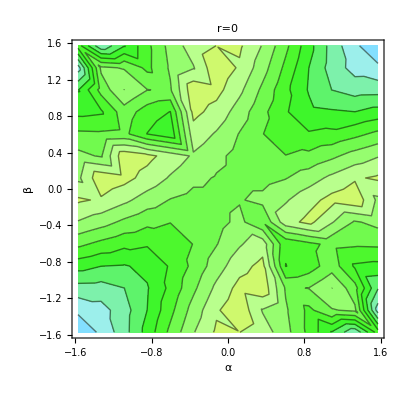

```mathematica
p1 = Ωfreeplot[0,0]
```

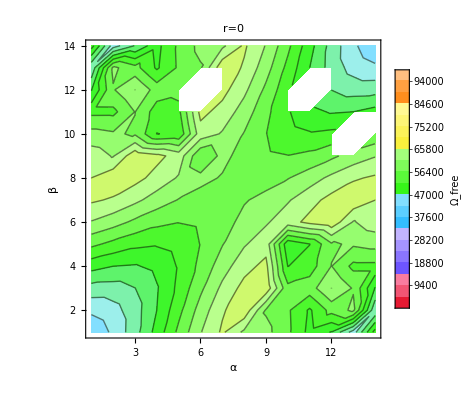

```mathematica
Legended[p1, BarLegend[{"BrightBands",{0,100000}},20,LegendMarkerSize->250, LegendLabel -> "Ω_free", LabelStyle -> {FontSize -> 20}]]
```

ArcTan::indet: Indeterminate expression ArcTan[0.,0.] encountered.

General::stop: Further output of ArcTan::indet will be suppressed during this calculation.

-Graphics-

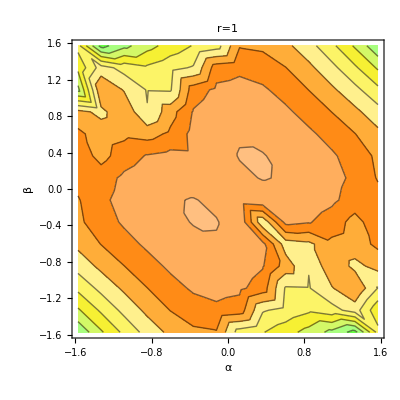

ArcTan::indet: Indeterminate expression ArcTan[0.,0.] encountered.

General::stop: Further output of ArcTan::indet will be suppressed during this calculation.

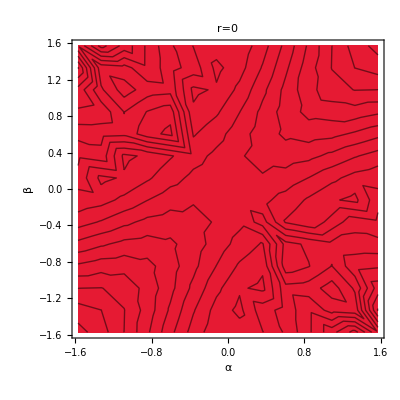

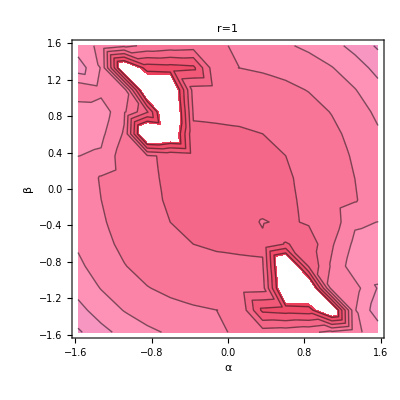

ArcTan::indet: Indeterminate expression ArcTan[0.,0.] encountered.

General::stop: Further output of ArcTan::indet will be suppressed during this calculation.

-Graphics-

ArcTan::indet: Indeterminate expression ArcTan[0.,0.] encountered.

General::stop: Further output of ArcTan::indet will be suppressed during this calculation.

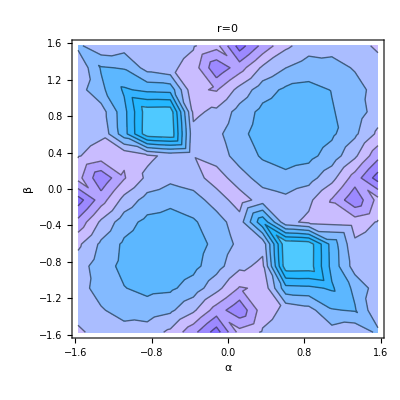

```mathematica
Ωfreeplot[0,0]
Ωfreeplot[1,0]
ΩfreeplotDEG[0,0]
ΩfreeplotDEG[1,0]
Ωfreeplot[0,0]
Ωfreeplot[0,2]
```

ArcTan::indet: Indeterminate expression ArcTan[0.,0.] encountered.

General::stop: Further output of ArcTan::indet will be suppressed during this calculation.

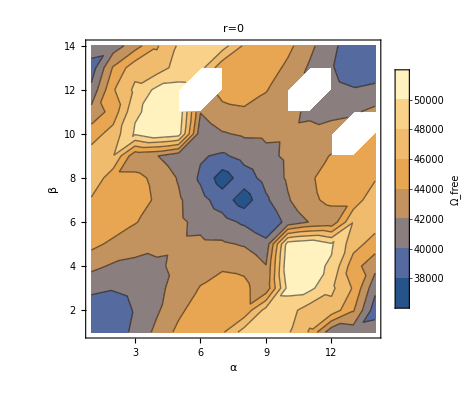

```mathematica
Ωfreeplot[0,10]
```

```mathematica
Effective Magnetic Field Vector Components
```

```mathematica
a=1; b= Pi/4;r=1;
```

```mathematica
a= Pi/4; b = -Pi/4; r= 1
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/10},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}}
Plot3D[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]/(0.7*el hbar/(2 me)) * 10^4*10^3,{a, -Pi/2, Pi/2},{b, -Pi/2, Pi/2},PlotLegends-> BarLegend[All,None,LegendMarkerSize->250, LegendLabel -> "|B_eff| (mG)", LabelStyle -> {FontSize -> 20}]]
```

1

{0,{x→-3.4084×10^-7,y→-4.2605×10^-7,zf→-2.5563×10^-7}}

-Graphics3D-

Direction of Δk

```mathematica
Δk = k({0,1,0}+{0,0,1}(1-r))
dirdelk = ToSphericalCoordinates[Δk]
```

{0.,7.37377×10^6,7.37377×10^6}

{1.04281×10^7,0.785398,1.5708}

```mathematica
Direction of Beff
```

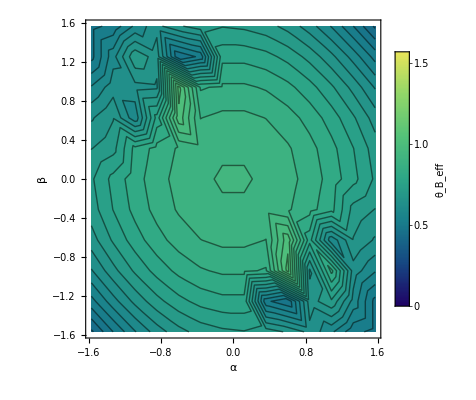

```mathematica
r=2.3;
ListContourPlot[ Flatten[Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/13},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}}; {a,b , ToSphericalCoordinates[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]][[2]]},{a, -Pi/2, Pi/2, Pi/13},{b, -Pi/2, Pi/2, Pi/10}],1], PlotLegends->BarLegend[{Automatic,{0,Pi/2}},None, LegendLabel-> "θ_B_eff"], FrameLabel->{"α","β"},ColorFunctionScaling->False, FrameStyle -> Black,InterpolationOrder->2,ColorFunction-> ColorData[{"BlueGreenYellow",{0, Pi/2}}], PlotRange->{ All, All, {0,Pi/2}}, Contours ->30, InterpolationOrder->5]
```

```mathematica
ToSphericalCoordinates[{0,-1,0}]
```

{1,π/2,-π/2}

```mathematica
ToSphericalCoordinates[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]][[2]]
```

1.34933

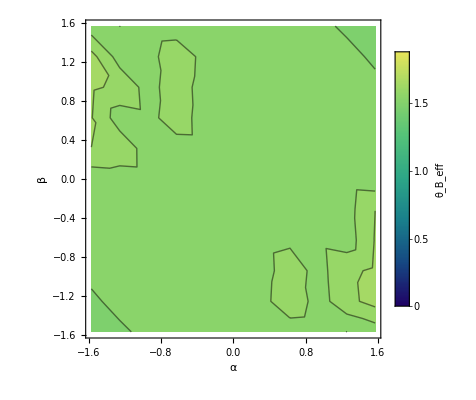
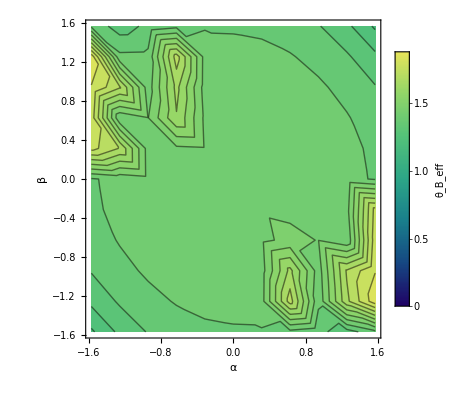
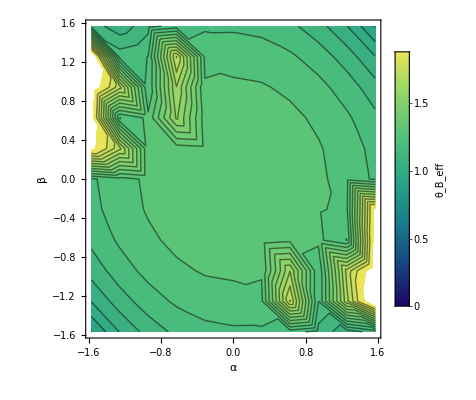
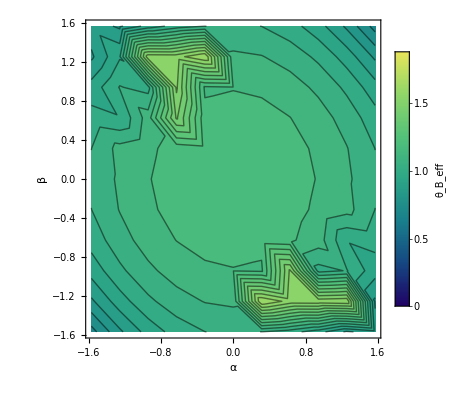
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Grid[{{
r=0.1;
ListContourPlot[ Flatten[Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/13},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}}; {a,b , ToSphericalCoordinates[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]][[2]]},{a, -Pi/2, Pi/2, Pi/10},{b, -Pi/2, Pi/2, Pi/10}],1], PlotLegends->BarLegend[{Automatic,{0,1.2Pi/2}},None, LegendLabel-> "θ_B_eff"], FrameLabel->{"α","β"},ColorFunctionScaling->False, FrameStyle -> Black,InterpolationOrder->2,ColorFunction-> ColorData[{"BlueGreenYellow",{0, 1.2Pi/2}}], PlotRange->{ All, All, {0,1.2Pi/2}}, Contours ->30, InterpolationOrder->5]
,

r=0.4;
ListContourPlot[ Flatten[Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/13},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}}; {a,b , ToSphericalCoordinates[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]][[2]]},{a, -Pi/2, Pi/2, Pi/10},{b, -Pi/2, Pi/2, Pi/10}],1], PlotLegends->BarLegend[{Automatic,{0,1.2Pi/2}},None, LegendLabel-> "θ_B_eff"], FrameLabel->{"α","β"},ColorFunctionScaling->False, FrameStyle -> Black,InterpolationOrder->2,ColorFunction-> ColorData[{"BlueGreenYellow",{0, 1.2Pi/2}}], PlotRange->{ All, All, {0,1.2Pi/2}}, Contours ->30, InterpolationOrder->5]
},
{

r=0.8;
ListContourPlot[ Flatten[Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/13},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}}; {a,b , ToSphericalCoordinates[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]][[2]]},{a, -Pi/2, Pi/2, Pi/10},{b, -Pi/2, Pi/2, Pi/10}],1], PlotLegends->BarLegend[{Automatic,{0,1.2Pi/2}},None, LegendLabel-> "θ_B_eff"], FrameLabel->{"α","β"},ColorFunctionScaling->False, FrameStyle -> Black,InterpolationOrder->2,ColorFunction-> ColorData[{"BlueGreenYellow",{0, 1.2Pi/2}}], PlotRange->{ All, All, {0,1.2Pi/2}}, Contours ->30, InterpolationOrder->5]
,

r=1.2;
ListContourPlot[ Flatten[Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/10},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}}; {a,b , ToSphericalCoordinates[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]][[2]]},{a, -Pi/2, Pi/2, Pi/10},{b, -Pi/2, Pi/2, Pi/10}],1], PlotLegends->BarLegend[{Automatic,{0,1.2Pi/2}},None, LegendLabel-> "θ_B_eff"], FrameLabel->{"α","β"},ColorFunctionScaling->False, FrameStyle -> Black,InterpolationOrder->2,ColorFunction-> ColorData[{"BlueGreenYellow",{0, 1.2Pi/2}}], PlotRange->{ All, All, {0,1.2Pi/2}}, Contours ->30, InterpolationOrder->5]


}}]
```

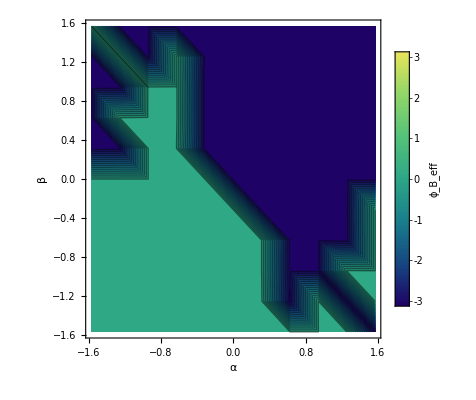
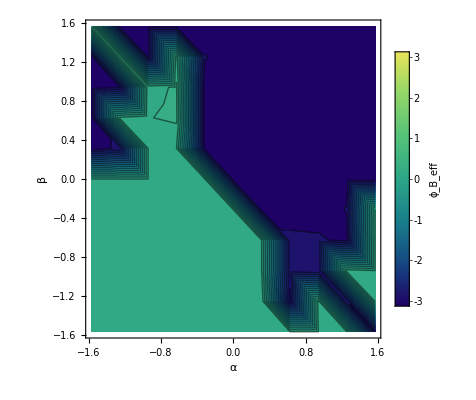
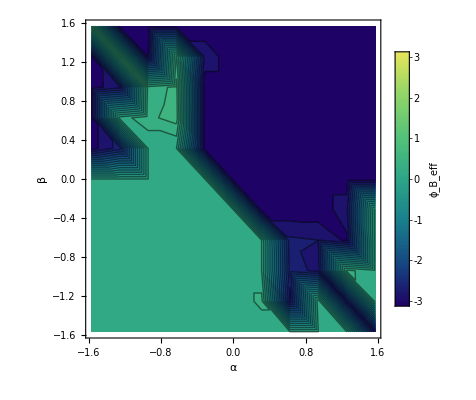
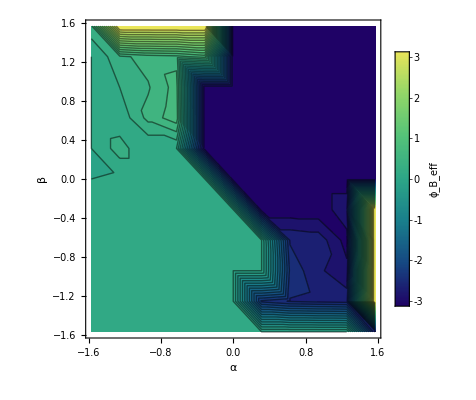
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Grid[{{
r=0.1;
ListContourPlot[ Flatten[Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/13},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}}; {a,b , ToSphericalCoordinates[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]][[3]]},{a, -Pi/2, Pi/2, Pi/10},{b, -Pi/2, Pi/2, Pi/10}],1], PlotLegends->BarLegend[{Automatic,{-Pi,Pi}},None, LegendLabel-> "ϕ_B_eff"], FrameLabel->{"α","β"},ColorFunctionScaling->False, FrameStyle -> Black,InterpolationOrder->2,ColorFunction-> ColorData[{"BlueGreenYellow",{-Pi,Pi}}], PlotRange->{ All, All, {-Pi,Pi}}, Contours ->30, InterpolationOrder->5]
,

r=0.4;
ListContourPlot[ Flatten[Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/13},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}}; {a,b , ToSphericalCoordinates[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]][[3]]},{a, -Pi/2, Pi/2, Pi/10},{b, -Pi/2, Pi/2, Pi/10}],1], PlotLegends->BarLegend[{Automatic,{-Pi,Pi}},None, LegendLabel-> "ϕ_B_eff"], FrameLabel->{"α","β"},ColorFunctionScaling->False, FrameStyle -> Black,InterpolationOrder->2,ColorFunction-> ColorData[{"BlueGreenYellow",{-Pi,Pi}}], PlotRange->{ All, All, {-Pi,Pi}}, Contours ->30, InterpolationOrder->5]
},
{

r=0.8;
ListContourPlot[ Flatten[Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/13},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}}; {a,b , ToSphericalCoordinates[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]][[3]]},{a, -Pi/2, Pi/2, Pi/10},{b, -Pi/2, Pi/2, Pi/10}],1], PlotLegends->BarLegend[{Automatic,{-Pi,Pi}},None, LegendLabel-> "ϕ_B_eff"], FrameLabel->{"α","β"},ColorFunctionScaling->False, FrameStyle -> Black,InterpolationOrder->2,ColorFunction-> ColorData[{"BlueGreenYellow",{-Pi,Pi}}], PlotRange->{ All, All, {-Pi,Pi}}, Contours ->30, InterpolationOrder->5]
,

r=1.2;
ListContourPlot[ Flatten[Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/10},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}}; {a,b , ToSphericalCoordinates[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]][[3]]},{a, -Pi/2, Pi/2, Pi/10},{b, -Pi/2, Pi/2, Pi/10}],1], PlotLegends->BarLegend[{Automatic,{-Pi,Pi}},None, LegendLabel-> "ϕ_B_eff"], FrameLabel->{"α","β"},ColorFunctionScaling->False, FrameStyle -> Black,InterpolationOrder->2,ColorFunction-> ColorData[{"BlueGreenYellow",{-Pi,Pi}}], PlotRange->{ All, All, {-Pi,Pi}}, Contours ->30, InterpolationOrder->5]}}]
```

ArcTan::indet: Indeterminate expression ArcTan[0.,0.] encountered.

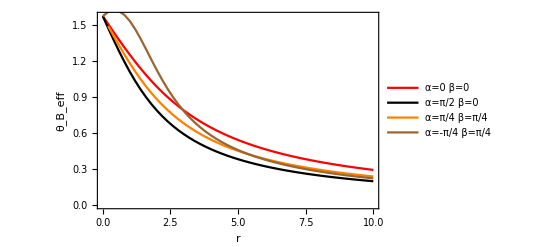

```mathematica
Show[{a= 0; b= 0;
ListLinePlot[ Flatten[Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/13},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}}; {r , ToSphericalCoordinates[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]][[2]]},{r, 0,10, 0.2}],0], FrameLabel->{"r","θ_B_eff"},PlotStyle ->Red, FrameStyle-> Black, Frame-> True,PlotLegends->Placed[LineLegend[{"α=0  β=0"}],Above]],
a= Pi/2; b= 0;
ListLinePlot[ Flatten[Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/13},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}}; {r , ToSphericalCoordinates[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]][[2]]},{r, 0,10, 0.2}],0], FrameLabel->{"r","θ_B_eff"},PlotStyle ->Black, FrameStyle-> Black, Frame-> True,PlotLegends->Placed[LineLegend[{"α=π/2  β=0"}],Above]],

a= Pi/4; b= Pi/4;
ListLinePlot[ Flatten[Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/13},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}}; {r , ToSphericalCoordinates[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]][[2]]},{r, 0,10, 0.2}],0], FrameLabel->{"r","θ_B_eff"},PlotStyle ->Orange, FrameStyle-> Black, Frame-> True, PlotLegends->Placed[LineLegend[{"α=π/4  β=π/4"}],Above]],


a= -Pi/4; b= Pi/4;
ListLinePlot[ Flatten[Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/13},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}}; {r , ToSphericalCoordinates[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]][[2]]},{r, 0,10, 0.2}],0], FrameLabel->{"r","θ_B_eff"},PlotStyle ->Brown, FrameStyle-> Black, Frame-> True,PlotLegends->Placed[LineLegend[{"α=-π/4  β=π/4"}],Above]]
}]
```

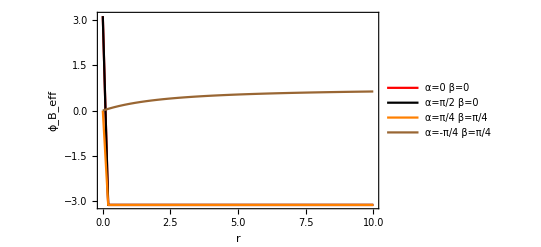

```mathematica
Show[{a= 0; b= 0;
ListLinePlot[ Flatten[Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/13},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}}; {r , ToSphericalCoordinates[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]][[3]]},{r, 0,10, 0.2}],0], FrameLabel->{"r","ϕ_B_eff"},PlotStyle ->Red, FrameStyle-> Black, Frame-> True,PlotLegends->Placed[LineLegend[{"α=0  β=0"}],Above]],
a= Pi/2; b= 0;
ListLinePlot[ Flatten[Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/13},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}}; {r , ToSphericalCoordinates[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]][[3]]},{r, 0,10, 0.2}],0], FrameLabel->{"r","ϕ_B_eff"},PlotStyle ->Black, FrameStyle-> Black, Frame-> True,PlotLegends->Placed[LineLegend[{"α=π/2  β=0"}],Above]],

a= Pi/3; b= Pi/3;
ListLinePlot[ Flatten[Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/13},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}}; {r , ToSphericalCoordinates[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]][[3]]},{r, 0,10, 0.2}],0], FrameLabel->{"r","ϕ_B_eff"},PlotStyle ->Orange, FrameStyle-> Black, Frame-> True, PlotLegends->Placed[LineLegend[{"α=π/4  β=π/4"}],Above]],


a= -Pi/3; b= Pi/4;
ListLinePlot[ Flatten[Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/13},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}}; {r , ToSphericalCoordinates[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]][[3]]},{r, 0,10, 0.2}],0], FrameLabel->{"r","ϕ_B_eff"},PlotStyle ->Brown, FrameStyle-> Black, Frame-> True,PlotLegends->Placed[LineLegend[{"α=-π/4  β=π/4"}],Above]]
}]
```

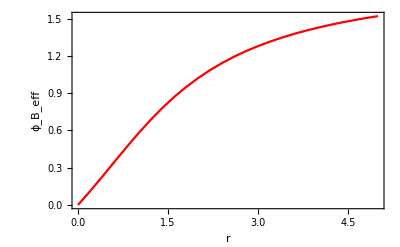

```mathematica
a= -Pi/4; b= Pi/4;
ListLinePlot[ Flatten[Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/13},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}}; {r , ToSphericalCoordinates[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]][[3]]},{r, 0,5, 0.2}],0], FrameLabel->{"r","ϕ_B_eff"},PlotStyle ->Red, FrameStyle-> Black, Frame-> True]
```

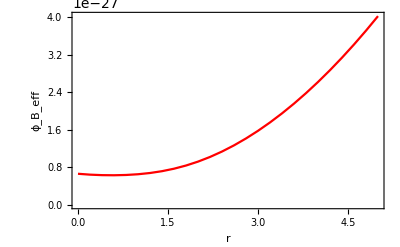

```mathematica
a= -Pi/4; b= Pi/4;
ListLinePlot[ Flatten[Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/13},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}}; {r , ToSphericalCoordinates[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]][[1]]},{r, 0,5, 0.2}],0], FrameLabel->{"r","ϕ_B_eff"},PlotStyle ->Red, FrameStyle-> Black, Frame-> True]
```

## new lattice potential (doesnt make sense as lattice stays the same in spite of the new beam!!!!!)

```mathematica
udsimraw = +-2/3*hbar Gam^2 Inti / (Delta*8 Ints)ϵ1.ϵ1s//FullSimplify
```

```mathematica
UDsim[x_,y_,z_,a_,b_]:=-1/(12 Delta Ints)Gam^2 hbar Inti (4+Cos[a-b-2 k x]+Cos[a-b+2 k x]+2 Cos[a] Cos[k (x-y)]+2 Cos[b] Cos[k (x+y)]+2 Cos[k (x+z)] Sin[b]+Sin[a+k x-k z]+Sin[a-k x+k z])
```

{0,{x→-4.2605×10^-7,y→-4.2605×10^-7,zf→-4.2605×10^-7}}

-Graphics3D-

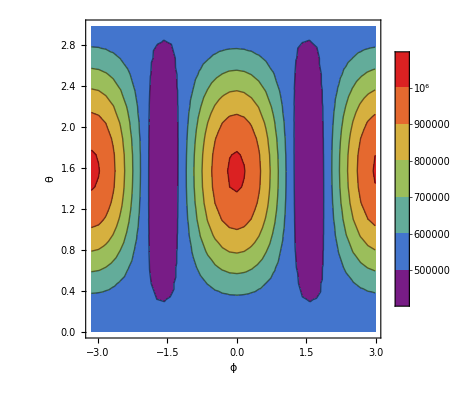

```mathematica
r=0;z=0;a= +Pi/4+Pi/18; +Pi/4+Pi/6;
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/10},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}}
goodlat = Show[{ListPlot3D[Flatten[Table[{x,y,Sqrt[ecrosss[x,y,zf /. mi[[2]],a,b].ecrosss[x,y,zf /. mi[[2]],a,b]]*2*10^28-13},{x,-2λ,2λ, λ/10},{y,-2 λ,2λ,λ/10}],1], PlotStyle ->  {LightRed, Opacity[0.7]}],

ListPlot3D[Flatten[Table[{x,y,UDsim[x,y,zf /. mi[[2]],a,b]/Er},{x,-2λ,2λ, λ/10},{y,-2 λ,2λ,λ/10}],1]]

}, PlotRange -> All]


ho = 10^-9;
x0=x/.mi[[2]]; y0=y/.mi[[2]]; z0=zf/.mi[[2]];
abola =Table[cart = FromSphericalCoordinates[{1,θ,ϕ}]//N;

{ϕ,θ,(Sqrt[1/mCs 1/ho^2(UDsim[x0+ ho cart[[1]],y0 +ho cart[[2]],z0 + ho cart[[3]],a,b]- 2UDsim[x0,y0 ,z0,a,b] + UDsim[x0-ho cart[[1]],y0 -ho cart[[2]],z0 - ho cart[[3]],a,b])])}

,{θ,0.0001 ,0.999 Pi, Pi/20},{ϕ,-Pi*0.999 , Pi, Pi/20}]; 
goodfreq = ListContourPlot[Flatten[abola,1], PlotLegends->True, ColorFunction-> "Rainbow", FrameLabel-> {"ϕ", "θ"}]
```

```mathematica
Flatten[Table[{x,y,ecrosss[x,y,zf /. mi[[2]],a,b].ecrosss[x,y,zf /. mi[[2]],a,b]},{x,-2λ,2λ, λ/10},{y,-2 λ,2λ,λ/10}],1]
```

{{-1.7042×10^-6,-1.7042×10^-6,5.17763×10^-55},{-1.7042×10^-6,-1.61899×10^-6,3.67475×10^-55},{-1.7042×10^-6,-1.53378×10^-6,2.45348×10^-55},1675,{1.7042×10^-6,1.53378×10^-6,5.36664×10^-55},{1.7042×10^-6,1.61899×10^-6,5.99758×10^-55},{1.7042×10^-6,1.7042×10^-6,5.17763×10^-55}}
 |  |  |  |

```mathematica
ListPlot3D[Flatten[Table[{x,y,UDsim[x,y,zf /. mi[[2]],a,b]/Er},{x,-2λ,2λ, λ/10},{y,-2 λ,2λ,λ/10}],1]]
```

-Graphics3D-